# Sistemas autónomos

## Ejemplo

Puntos de equilibrio en el retrato fase:

```mathematica
Solve[{0==(y-x)*(1-x-y),0==x*(2+y)},{x,y}]
```

{{x→-2,y→-2},{x→0,y→0},{x→0,y→1},{x→3,y→-2}}

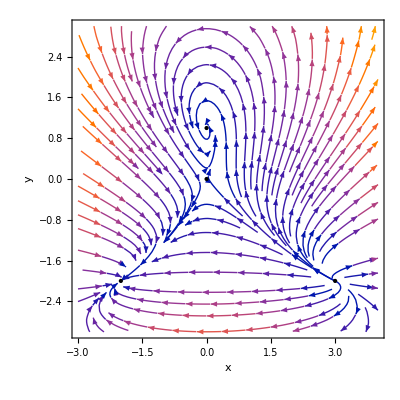

```mathematica
sp1=StreamPlot[{(y-x)*(1-x-y),x*(2+y)},{x,-3,4},{y,-3,3},FrameLabel->{x,y},Epilog->{Black,PointSize@Large,Point[{{-2,-2},{0,0},{0,1},{3,-2}}]}]
```

Nos acercamos para saber cómo se ven los puntos de equilibrio localmente:

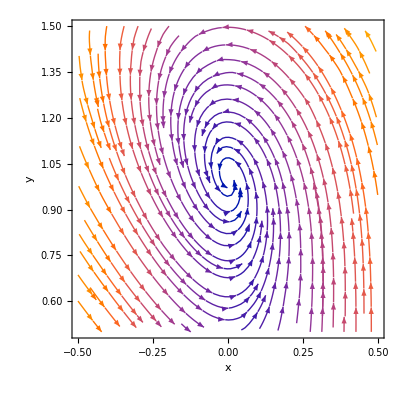

```mathematica
StreamPlot[{(y-x)*(1-x-y),x*(2+y)},{x,-0.5,0.5},{y,0.5,1.5},FrameLabel->{x,y}]
```

El  es una espiral estable.

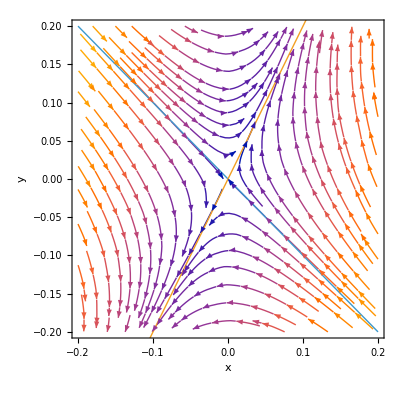

```mathematica
Show[StreamPlot[{(y-x)*(1-x-y),x*(2+y)},{x,-0.2,0.2},{y,-0.2,0.2},FrameLabel->{x,y}],Plot[{-x,2*x},{x,-0.2,0.2},PlotStyle->Thick]]
```

El  es un punto silla.

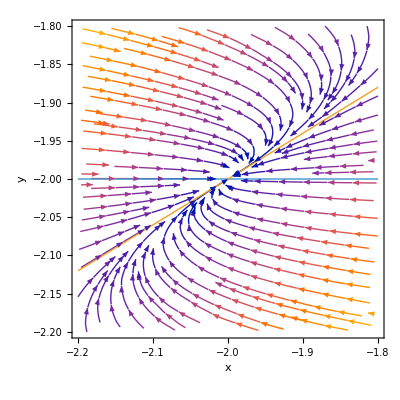

```mathematica
Show[StreamPlot[{(y-x)*(1-x-y),x*(2+y)},{x,-2.2,-1.8},{y,-2.2,-1.8},FrameLabel->{x,y}],Plot[{-2,3*x/5-4/5},{x,-2.2,-1.8},PlotStyle->Thick]]
```

El  es un nodo estable.

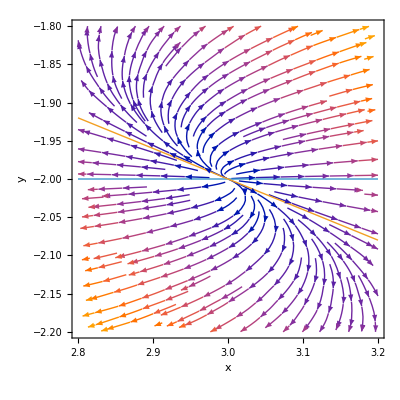

```mathematica
Show[StreamPlot[{(y-x)*(1-x-y),x*(2+y)},{x,2.8,3.2},{y,-2.2,-1.8},FrameLabel->{x,y}],Plot[{-2,-2*x/5-4/5},{x,2.8,3.2},PlotStyle->Thick]]
```

El  es un nodo inestable.
Además, hay dos soluciones importantes del sistema no lineal, que podemos ver en la gráfica de abajo:

```mathematica
hcl1=NDSolve[{x'[t]==(y[t]-x[t])*(1-x[t]-y[t]),y'[t]==x[t]*(2+y[t]),x[1000]==-0.01,y[1000]==0.01},{x,y},{t,0,1000}];
hcl2=NDSolve[{x'[t]==(y[t]-x[t])*(1-x[t]-y[t]),y'[t]==x[t]*(2+y[t]),x[1000]==0.01,y[1000]==-0.01},{x,y},{t,0,1000}];
hcl3=NDSolve[{x'[t]==(y[t]-x[t])*(1-x[t]-y[t]),y'[t]==x[t]*(2+y[t]),x[1000]==-1,y[1000]==-1},{x,y},{t,0,1000}];
```

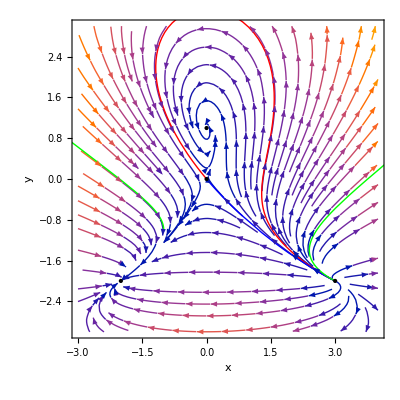

```mathematica
Show[{sp1,ParametricPlot[Evaluate[{x[t],y[t]}/.hcl1],{t,0,1000},PlotStyle->{Red,Thick},PlotPoints->700],ParametricPlot[Evaluate[{x[t],y[t]}/.hcl2],{t,0,1000},PlotStyle->{Blue,Thick},PlotPoints->700],
ParametricPlot[Evaluate[{x[t],y[t]}/.hcl3],{t,0,1000},PlotStyle->{Green,Thick},PlotPoints->700]}]
```

Estas soluciones corresponden a las variedades estables del punto silla . En este contexto, estas soluciones se llaman separatrices, pues separan al espacio fase en diferentes cuencas de atracción. Es decir, definen los subconjuntos de condiciones iniciales que resultan en su atracción hacia diferentes puntos de equilibrio.
Veamos como la siguiente solución es atraída hacia la espiral estable, el , al estar dentro de la cuenca de atracción de éste:

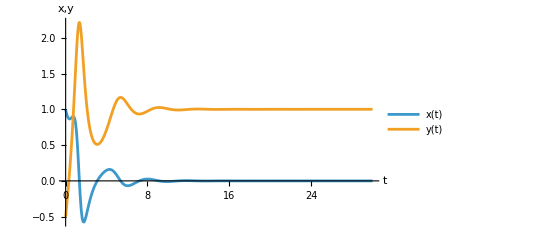

```mathematica
sol1=NDSolve[{x'[t]==(y[t]-x[t])*(1-x[t]-y[t]),y'[t]==x[t]*(2+y[t]),x[0]==1,y[0]==-0.5},{x,y},{t,0,30}];
Plot[Evaluate[{x[t],y[t]}/.sol1],{t,0,30},AxesLabel->{t,"x,y"},PlotLegends->{x[t],y[t]}]
```

Si ahora elegimos una condición inicial en la cuenca de atracción del nodo estable, el , las soluciones se acercan asintóticamente a este punto:

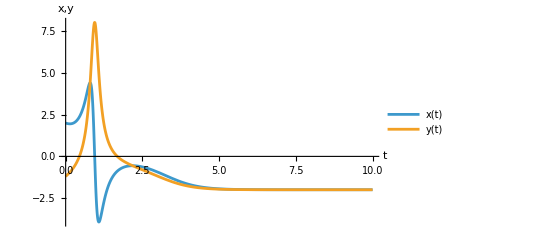

```mathematica
sol2=NDSolve[{x'[t]==(y[t]-x[t])*(1-x[t]-y[t]),y'[t]==x[t]*(2+y[t]),x[0]==2,y[0]==-1.2},{x,y},{t,0,10}];
Plot[Evaluate[{x[t],y[t]}/.sol2],{t,0,10},AxesLabel->{t,"x,y"},PlotLegends->{x[t],y[t]},PlotRange->All]
```